{{x[t]→(ⅇ^(-2 t γ) (F-ⅇ^(2 t γ) F+2 ⅇ^(2 t γ) F t γ-2 v0 γ+2 ⅇ^(2 t γ) v0 γ+4 ⅇ^(2 t γ) x0 γ^2))/(4 γ^2)}}

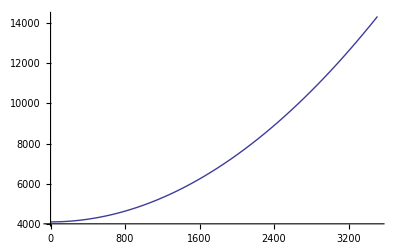

```mathematica
ClearAll["Global`*"]
ω=0;
(*x0=4096;
γ=4.6215857993096394*10^-6;
F= 0.0016791886002948619;*)
(*γ=0;*)
f=DSolve[{x''[t]+2γ x'[t]+ω^2 x[t]-F==0,
x[0]==x0,
x'[0]==v0}
,x[t],t ]
Plot[Evaluate[x[t]/.f/.{
{γ->4.6215857993096394*^-6,ω-> 0.0001,F-> 0.0016791886002948619,x0-> 4096,v0->0}
}]
,{t,0,3511}]
```

```mathematica
times={0,56,121,186,251,317,382,447,512,577,643,708,773,838,903,969,1034,1099,1164,1229,1295,1360,1425,1490,1555,1621,1686,1751,1816,1881,1947,2012,2077,2142,2207,2273,2338,2403,2468,2533,2599,2664,2729,2794,2859,2925,2990,3055,3120,3185,3251,3316,3446,3511,3577,3642,3707,3772,3837,3903,3968,4033,4098,4163,4229,4294,4359,4424,4489,4555,4620,4685,4750,4815,4881,4946,5011,5076,5141,5207,5272};
usignal={100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
coords={4083,4083,4084,4092,4099,4129,4177,4207,4279,4363,4410,4511,4564,4677,4795,4858,4991,5138,5219,5392,5579,5676,5874,6076,6180,6392,6499,6712,6928,7043,7293,7572,7717,8005,8294,8438,8725,8866,9165,9508,9691,10057,10417,10595,10941,11308,11513,11942,12153,12565,12959,13154,13584,14268,14699,15071,15235,15535,15777,15872,16000,16038,16062,16037,16015,15957,15891,15856,15784,15714,15682,15628,15608,15584,15581,15586,15595,15595,15593,15589,15592};
stopInd=Position[usignal,0]⟦1⟧⟦1⟧;
```

1/4 (16384+(F (-1+ⅇ^(-2 t γ)+2 t γ))/γ^2)

1/4 (16384+(F (-1+ⅇ^(-6892 γ)+6892 γ))/γ^2)

(F (2 γ-2 ⅇ^(-6892 γ) γ))/(4 γ^2)

4096+(F (-ⅇ^(-2 t γ)+ⅇ^(-2 (3446+t) γ)+6892 γ))/(4 γ^2)

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.000401739, 3.65252, 0.00022394}, is returned.

{γ→8.64165×10^-6,F→0.00169472}

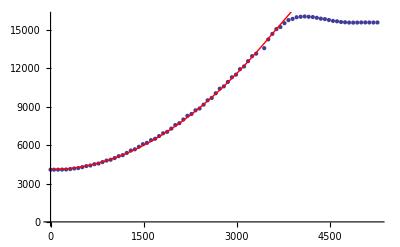

```mathematica
testData1=Transpose[{times⟦1;;stopInd⟧,coords⟦1;;stopInd⟧}];
testData=Transpose[{times,coords}];

(*x0=4096;*)
(*γ=1E-1;*)
ω=1;
motion=FullSimplify[Evaluate[x[t]/.f/.{v0->0,x0->4096}]⟦1⟧]
xFinal=Evaluate[motion/.{t->times⟦stopInd⟧}]
vFinal=Evaluate[D[motion,t]/.{t->times⟦stopInd⟧}]
inertion=FullSimplify[Evaluate[x[t]/.f/.{F->0,v0->vFinal,x0->xFinal}]⟦1⟧]
model=Piecewise[{{motion,t≤ times⟦stopInd⟧},{Evaluate[inertion/.{t->t- times⟦stopInd⟧}],t> times⟦stopInd⟧}}];

fit=FindFit[testData1,{model,γ>0,F>0},{{γ,0.0001},{F, 0.000014}},t]
Show[
ListPlot[testData],
Plot[model/.fit,{t,0,Max[times]}
,PlotStyle->{Red,Thick}
]
]
```

-1.9648×10^7+1.96521×10^7 ⅇ^(-9.24317×10^-6 t)+181.648 t

13960.

5.69466

630054.-616094. ⅇ^(-9.24317×10^-6 t)

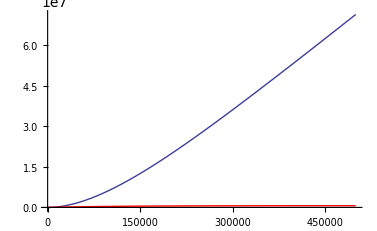

```mathematica
Clear[γ,F,model]
γ=4.6215857993096394*10^-6;
(*F= 0.0016791886002948619;*)
motion=FullSimplify[Evaluate[x[t]/.f/.{F->0.001679,v0->0,x0->4096}]⟦1⟧]
xFinal=Evaluate[motion/.{t->times⟦stopInd⟧}]
vFinal=Evaluate[D[motion,t]/.{t->times⟦stopInd⟧}]
inertion=FullSimplify[Evaluate[x[t]/.f/.{F->0,v0->vFinal,x0->xFinal}]⟦1⟧]
model=Piecewise[{{motion,t≤ times⟦stopInd⟧},{Evaluate[inertion/.{t->t- times⟦stopInd⟧}],t> times⟦stopInd⟧}}];

Show[
Plot[motion,{t,0,500000}]
,Plot[model,{t,0,500000},PlotStyle->Red]
]
```

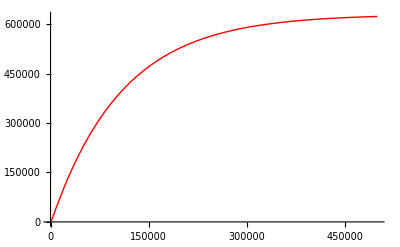

```mathematica
Plot[model,{t,0,500000},PlotStyle->Red]
```